# An Introduction to Mathematica, pt.2

## Mathematica Vernacular: The Anatomy of Expressions

## “Standard” vs. “Non-Standard” expressions

### “Standard” expressions: function[x,y,...,z]

This is the way that all expressions are handled internally by Mathematica, and 
all functions can be called in this way— 
(even if a non-standard form is more familiar or more often used). 
Knowing this will help us understand how to manipulate formulae symbolically.

#### In the expression “function[x,y,...,z]”, “function” is called the Head

```mathematica
Head[function[x,y,z]]
```

function

#### The Head of the outer-most function of any expression is its “0th Part”:

```mathematica
Part[function[x,y,z],0]
```

function

or, equivalently,

```mathematica
function[x,y,z][[0]]
```

function

#### Even atomic expressions have Heads—corresponding to their type:

```mathematica
Head[x]
Head[1]
Head[1.]
Head[3/4]
Head[1+ⅈ]
```

Symbol

Integer

Real

Rational

Complex

#### The “Standard” form of any expression can be found by calling for FullForm:

```mathematica
FullForm[((x+y+z)*w)^(q/r)]
```

Power[Times[w,Plus[x,y,z]],Times[q,Power[r,-1]]]

This can be converted back to a more human-readable form via StandardForm, InputForm, or TraditionalForm

```mathematica
StandardForm[Power[Times[w,Plus[x,y,z]],Times[q,Power[r,-1]]]]
TraditionalForm[Power[Times[w,Plus[x,y,z]],Times[q,Power[r,-1]]]]
InputForm[Power[Times[w,Plus[x,y,z]],Times[q,Power[r,-1]]]]
```

(w (x+y+z))^(q/r)

(w (x+y+z))^(q/r)

(w*(x + y + z))^(q/r)

If you’re ever worried about the order in which Mathematica performs its operations, use FullForm

The nested structure of the expression is nicely illustrated by the function: TreeForm

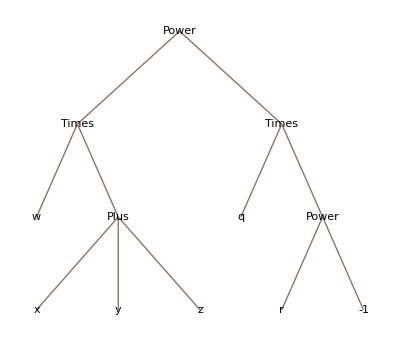

```mathematica
TreeForm[((x+y+z)*w)^(q/r)]
```

```mathematica
Head[((x+y+z)*w)^(q/r)]
FullForm[((x+y+z)*w)^(q/r)]
```

Power

Power[Times[w,Plus[x,y,z]],Times[q,Power[r,-1]]]

#### The number of vertices of such a tree graph is a measure of an expression’s complexity, and this is counted by the function LeafCount

```mathematica
LeafCount[((x+y+z)*w)^(q/r)]
```

12

Many functions, such as FullSimplify use LeafCount as their (principle) metric for complexity. Output with a LeafCount above a few thousand are essentially unreadable.

#### Notice that arguments of functions are always enclosed within square brackets. Thus,

```mathematica
Sin(π)
```

π Sin

is interpreted as multiplication of the symbol “Sin” by “π” (although “Sin[]” is a built-in function, it is only defined when it has been given an argument).

We can confirm that this is indeed how Mathematica interprets it using FullForm:

```mathematica
FullForm[Sin(π)]
```

Times[Pi,Sin]

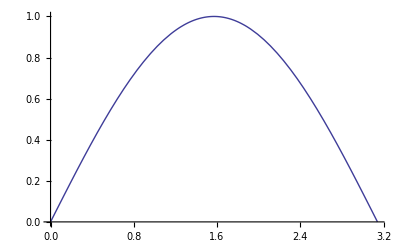

```mathematica
Plot[Sin[Sin],{Sin,0,π}]
```

### Infix notation “ x ∘ y ∘ ... ∘ z “ : the most typical “Non-Standard” form for expressions

Infix notation is used to write “function[x,y,...,z]” in the form “x ∘ y ∘ ... ∘ z” where “ ∘ “ is a symbol associated with “function”.

(Any function can be called in this way, but it is rarely advisable to define your functions in this form).

Although all functions are treated internally by Mathematica (and hence can be used) in the “Standard” form described above, there are a few functions which are almost always written by users in Infix form. Most of these should be very familiar—and we only make note of them here to highlight their unfamiliar but standard forms.

#### Commonly Infixed mathematical operations:

x * y * ... * z  :: Times[x,y,...,z]  (“␣” can be used interchangably with “*”)

x + y + ... + z  :: Plus[x,y,...,z]

Notice, however, that “ x - y “ is not “an Infix form of “Minus”” (no such function exists!)

```mathematica
x-y
FullForm[%]
(x-y)[[2,1]]
```

x-y

Plus[x,Times[-1,y]]

-1

#### Commonly Infixed functorial operations:

x = y  ::  Set[x,y]      (or     f[x] = y :: Set[f[x], y]     or     f[x_] = y :: Set[f[x_],y] )

Like many built-in fuctions, Set can have an arbitrary number of arguments—
but it is not commutative! (Just as “Power[x,y]” is not commutative). 
This is one main disadvantage to using Infix notation.

The other main `functorial’ operations similarly have Standard forms.

x := y  ::  SetDelayed[x,y]     (or     f[x_] := y  ::  SetDelayed[f[x_],y]   or ...)

x -> y  ::  Rule[x,y]    (or   f[x] -> y  ::  Rule[f[x],y]   or   f[x_] -> y  ::  Rule[f[x_],y] )

x :> y  ::  RuleDelayed[x,y]    (or  f[x_] -> y  ::  RuleDelayed[f[x_],y]     or  ... )

#### Commonly Infixed logical tests and logical operations

x == y == ... == z  ::  Equal[x,y,...,z]

Equal returns True or False if two things are “equal”, and is unevaluated if the answer is unknown

```mathematica
Equal[x,y]
FullForm[%]
x==1
```

x==y

Equal[x,y]

x==1

Similarly,

```mathematica
x==1
```

x==1

because x is undefined, Mathematica does not know if “x equals 1” or not, and therefore returns neither True nor False, but rather leaves the expression un-evaluated.

Notice that two differently-ordered sets (Lists) are not considered Equal

False

False

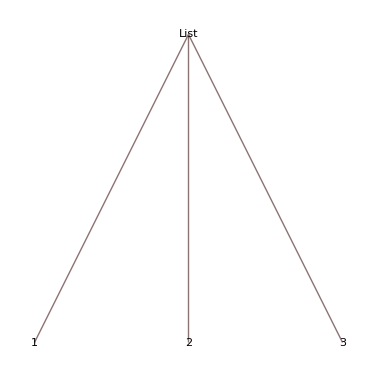
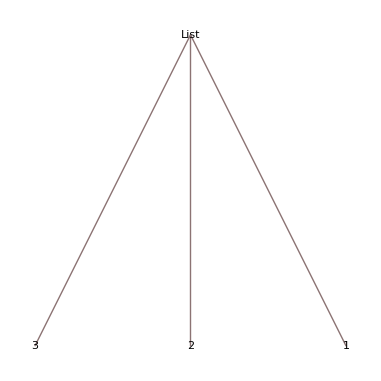

```mathematica
{1,2,3}=={3,2,1}
Equal@@{{1,2,3},{3,2,1}}
TreeForm/@{{1,2,3},{3,2,1}}
```

x === y === ... === z :: SameQ[x,y,...,z]

SameQ is a much stronger test than Equal: it tests whether two expressions are 
manifestly identical (or, (in a less-precisely-clear sense) “algebraically identical”)

```mathematica
x===y
```

False

To see how “Equal” and “SameQ” differ, consider the following:

```mathematica
1==1.
1===1.
```

True

False

The reason why is easily seen from the fact that “1” is an Integer while “1.” is a Real number:

```mathematica
Head[1]
Head[1.]
```

Integer

Real

```mathematica
Sin[π]===0
FullForm[Sin[π]]
```

True

0

x  > y > ... > z :: Greater[x,y,...,z]

x >= y >= ... >= z :: GreaterEqual[x,y,...,z]

```mathematica
x>y>z
FullForm[%]
```

x>y>z

Greater[x,y,z]

x && y && ... && z  :: And[x,y,...,z]

x || y || ... || z  :: Or[x,y,...,z]

```mathematica
x&&y&&z
FullForm[%]
x||y||z
FullForm[%]
```

```mathematica
(x≤y)&&(y<x)
FullForm[%]
```

x≤y&&y<x

And[LessEqual[x,y],Less[y,x]]

```mathematica
FullForm[%]
FullSimplify[(x≤y)&&(y<x)]
```

And[LessEqual[x,y],Less[y,x]]

False

#### Other common encounters with Infix notation

x <> y <> ... <> z  ::  StringJoin[x,y,...,z]

```mathematica
"honorific"<>"abilitud"<>"initatibus"
FullForm[Hold["honorific"<>"abilitud"<>"initatibus"]]
```

honorificabilitudinitatibus

Hold[StringJoin["honorific","abilitud","initatibus"]]

x | y | ... | z  :: Alternatives[x,y,...,z]

Alternatives[x,y,..,z] represents a (meta-)pattern, which can be any one of the patterns x, y, ..., or z.

(If you’ve ever tried to combine patterns with “Or” when using Cases or Position, this was the function you were looking for.)

```mathematica
Cases[{1,2,3,4,5,a,x,y,Sin[x]},_Integer|_Symbol]
Cases[{1,2,3,4,5,a,x,y,Sin[x]},Alternatives@@{_Integer,_Symbol}]
```

{1,2,3,4,5,a,x,y}

{1,2,3,4,5,a,x,y}

### Behind-the-scenes Functions

#### The function “List[x,y,...,z]” can also be written “{x,y,...,z}”

```mathematica
{1,2,3,4}
FullForm[%]
AngleBracket[1,2,3,4]
```

{1,2,3,4}

List[1,2,3,4]

⟨1,2,3,4⟩

```mathematica
??I
```

I represents the imaginary unit SqrtBox[RowBox[{"-", "1"}]].

Attributes[ⅈ]={Locked,Protected,ReadProtected}

Nota Bene: Matrices are just Lists of Lists (which have uniform lengths)

```mathematica
({{a, b, c}, {d, e, f}})
FullForm[%]
```

{{a,b,c},{d,e,f}}

List[List[a,b,c],List[d,e,f]]

#### expression[[x,y,...,z]] :: Part[expression, x,y,...,z]

It is often thought that the notation “[[ j ]]” is used in Mathematica to mean “the jth entry of a list”. While it is true that the jth part of the expression List[x,y,...,z] is the list’s jth entry, this understanding of the notation does not make clear how broadly applicable these double-square brackets are in Mathematica.

Because all expressions, are ultimately just nested Standard Expressions in disguise, every sub-part of every expression in Mathematica has its own unique “address”, and can be accessed using Part

1/2 ⅇ^(x y z)

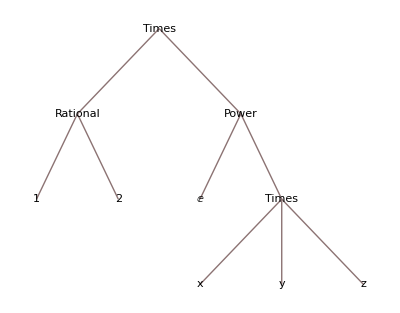

```mathematica
1/2Exp[x y z]
TreeForm[1/2Exp[x y z]]
```

```mathematica
Part[1/2Exp[x y z],0]
(1/2Exp[x y z])[[0]]
```

Times

Times

```mathematica
(1/2Exp[x y z])[[1]]
(1/2Exp[x y z])[[2]]
(1/2Exp[x y z])[[2,1]]
(1/2Exp[x y z])[[2,2]]
```

1/2

ⅇ^(x y z)

ⅇ

x y z

The “address” of any particular sub-expression can be found using Position:

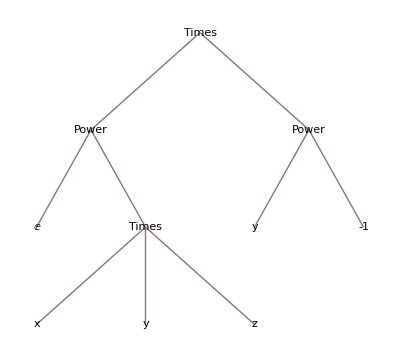

```mathematica
TreeForm[(1/y Exp[x y z])]
```

```mathematica
Position[(1/y Exp[x y z]),y]
```

{{1,2,2},{2,1}}

```mathematica
Part[(1/2Exp[x y z]),2,2,2]
(* Equivalently, *)
(1/2Exp[x y z])[[2,2,2]]
```

y

y

### Connections between functions and their arguments

#### Prefix notation: f @ x :: f[x]

```mathematica
f@x
FullForm[%]
```

f[x]

f[x]

#### Postfix notation: x // f :: f[x]

```mathematica
x//f
```

f[x]

```mathematica
{a,b,c}/.{a->5}
```

{5,b,c}

#### Apply is often written in a prefix-like notation: f@@{x,y,...,z} :: f[x,y,...,z] :: Apply[f,{x,y,...,z}]

```mathematica
TreeForm[g[1,2,3,4,5]];
f@@{1,2,3,4,5}
f[Sequence@@{1,2,3,4,5}]
```

f[1,2,3,4,5]

f[1,2,3,4,5]

#### Another variant of Apply, is also frequently encountered: f@@@{{a,b,...,c},...,{x,y,...,z}} :: {f[a,b,...,c],...,f[x,y,..,z]} :: Apply[f, {{a,b,...,c},...,{x,y,...,z}},{1}]

```mathematica
f@@@{{a,b,c},{x,y,z}}
Apply[f,{{a,b,c},{x,y,z}},{0}]
```

{f[a,b,c],f[x,y,z]}

f[{a,b,c},{x,y,z}]

#### Map is similarly often written in a prefix-like notation: f/@{x,y,...,z} :: {f[x],f[y],...,f[z]} :: Map[f,{x,y,...,z}]

```mathematica
f/@{a,b,c,1,2,3}
```

{f[a],f[b],f[c],f[1],f[2],f[3]}

```mathematica
(#/@{a,b,c,1,2,3})&/@{f,g,h}
```

{{f[a],f[b],f[c],f[1],f[2],f[3]},{g[a],g[b],g[c],g[1],g[2],g[3]},{h[a],h[b],h[c],h[1],h[2],h[3]}}

```mathematica
f@@{a,b,c,1,2,3}
```

f[a,b,c,1,2,3]

```mathematica
f/@{{a,b,c},{x,y,z}}
f@@@{{a,b,c},{x,y,z}}
f@@#&/@{{a,b,c},{x,y,z}}
```

{f[{a,b,c}],f[{x,y,z}]}

{f[a,b,c],f[x,y,z]}

{f[a,b,c],f[x,y,z]}

```mathematica
Table[f[j],{j,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
IntegerQ[n]
```

False

```mathematica
?Assumptions
```

Assumptions is an option for functions such as Simplify, Refine and Integrate which specifies default assumptions to be made about symbolic quantities.

## Functions and Forms to Become (very) Friendly With

### Patterns and Tests

#### “x_y” :: “a single-length pattern named herein as x (optional), with Head y (optional)

```mathematica
matrix={{1,α[x]+α[10],α[8] α[10],-α[11],-α[5] α[11],α[12],α[2] α[12],0},{0,1,α[8],α[6]+α[7],α[5] α[7],0,0,0},{0,0,0,1,α[5],α[3]+α[4],α[2] α[4],0},{0,0,0,0,0,1,α[2],α[1]}};
MatrixForm[%]
Cases[matrix,α[x_Integer],3]
MatrixForm[matrix/.{α[x_]:>Subscript[α,x]}]
MatrixForm[matrix/.{x_α:>Subscript[α,x[[0]]]}]
```

(1 | α[10]+α[x] | α[8] α[10] | -α[11] | -α[5] α[11] | α[12] | α[2] α[12] | 0
0 | 1 | α[8] | α[6]+α[7] | α[5] α[7] | 0 | 0 | 0
0 | 0 | 0 | 1 | α[5] | α[3]+α[4] | α[2] α[4] | 0
0 | 0 | 0 | 0 | 0 | 1 | α[2] | α[1])

{α[10],α[8],α[10],α[11],α[5],α[11],α[12],α[2],α[12],α[8],α[6],α[7],α[5],α[7],α[5],α[3],α[4],α[2],α[4],α[2],α[1]}

(1 | α_10+α_x | α_8 α_10 | -α_11 | -α_5 α_11 | α_12 | α_2 α_12 | 0
0 | 1 | α_8 | α_6+α_7 | α_5 α_7 | 0 | 0 | 0
0 | 0 | 0 | 1 | α_5 | α_3+α_4 | α_2 α_4 | 0
0 | 0 | 0 | 0 | 0 | 1 | α_2 | α_1)

(1 | 2 α_α | α_α^2 | -α_α | -α_α^2 | α_α | α_α^2 | 0
0 | 1 | α_α | 2 α_α | α_α^2 | 0 | 0 | 0
0 | 0 | 0 | 1 | α_α | 2 α_α | α_α^2 | 0
0 | 0 | 0 | 0 | 0 | 1 | α_α | α_α)

```mathematica
MatrixForm[matrix/.{α[x_]:>Subscript[α,x]}]
MatrixForm[matrix/.{x_α:>Subscript[α,x[[1]]]}]
Cases[matrix,_α,3]
Cases[matrix,_Integer,∞]
```

#### “x _ _ y” :: “an arbitrary-(but non-empty)-length pattern named herein as x with Head y

#### “x _ _ _ y” :: “an arbitrary-length (including zero) pattern named heren as x with Head y

#### “x_:default” :: a pattern which takes-on the default value of default

```mathematica
myFunction[x_:10]:=x^2
```

```mathematica
myFunction[3]
```

9

#### “x_?(testFunction)” :: a pattern for which testFunction[x]==True

```mathematica
Cases[matrix,α[_],∞]
```

{α[10],α[x],α[8],α[10],α[11],α[5],α[11],α[12],α[2],α[12],α[8],α[6],α[7],α[5],α[7],α[5],α[3],α[4],α[2],α[4],α[2],α[1]}

```mathematica
greaterThanTen[x_]:=x>10;
Cases[matrix,α[x_?greaterThanTen],∞]
```

```mathematica
Cases[matrix,α[x_?(#>10&)],∞]
```

{α[11],α[11],α[12],α[12]}

### Pure Functions

#### Function[{x,y,...,z},(expression involving x,y,...,z)]

This is a `pure function:’ and does store any permanent `pointer’ to itself in memory.

```mathematica
Function[{x,y,z},x y z]@@{1,2,3}
```

6

This is equivalent to:

#### (expression involving the variable `#’ )&, or (expression involving the variables #1,#2,...,#3 )&

```mathematica
((#1^2+#2^3+#3^4)&)@@@{{1,2,3},{a,b,c}}
```

{90,a^2+b^3+c^4}

### Applying Functions

#### Map and MapIndexed

#### Apply

#### Thread

```mathematica
Variables[matrix]
```

```mathematica
explicify[exprn_]:=(exprn/.Thread[Rule[Variables[exprn],RandomInteger[500,Length[Variables[exprn]]]]]);
explicify[matrix]
```

#### Nest, NestList, FixedPoint

### Blocks and Modules (Block vs. Module)

#### Block[{n=10,k=5,function[x_]=(...),...}, (some collection of expressions involving the local variables]

```mathematica
ephemeralVariable=19
Block[{ephemeralVariable},ephemeralVariable]
```

```mathematica
Block[{ephemeralVariable=17},ephemeralVariable]
ephemeralVariable
```

(Similar to, but more flexible than “With[{},...]”)

Use Blocks to define complex functions where some collection of intermediate-level functions are needed (but which are specialized to the task at hand.

#### Module[{n=10,k=5,function[x_]=(...),...}, (some collection of expressions involving the local variables]

Roughly similar to Block, but in detail more similar to the kind of “local variable” scoping familiar in less objective programming languages

```mathematica
ephemeralVariable=19
Module[{ephemeralVariable},ephemeralVariable]
```

19

ephemeralVariable$1829

Notice that in Module, the variable “ephemeralVariable” is truly local—indeed, it is handled internally with a unqiue name/pointer.

#### Many functions that you probably use all the time are really Blocks:

Table[(function of the local variable “j”),{“j”,...}]

Sum[(function of the local variable “j”),{“j”,...}]

Product[(function of the local variable “j”),{“j”,...}]

Integrate[(function of the local variable “j”),{“j”,...}]

etc.

### List (and Expression) Manipulation: Filtering, Structuring, Ordering, etc.

#### Sort and Ordering

#### Select

#### Position

#### Part , Drop, Take

#### Flatten

#### PadRight, PadLeft and ArrayPad

#### RotateLeft, RotateRight

#### Partition

#### Row

```mathematica
Range[4]
Row[%]
```

### Iterators and Generating Lists

#### Table

Notice: the iterator, say j, need not run over a range of integers: using {j,list}, j will take on each of the successive entries in the list list.

#### Array and SparseArray

#### For

#### Do

#### While

#### MapIndexed